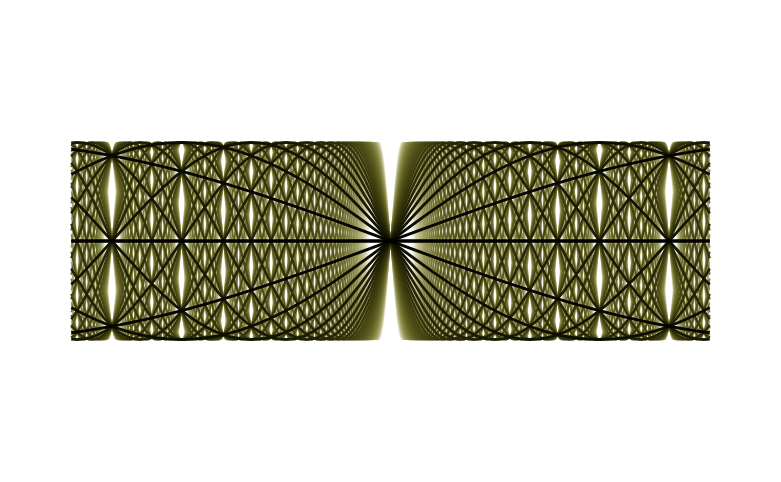

```mathematica
Plot[Evaluate[Table[{Sin[6*(1-0.025n)x],-Sin[6*(1-0.025n)x]},{n,40}]],{x,-8,8},PlotRange->2,Axes->False,PlotStyle->Flatten[Table[{{Thickness[0.00007n],RGBColor[1-n/40,1-n/40,(1-n/40)^2]},{Thickness[0.00007n],RGBColor[1-n/40,1-n/40,(1-n/40)^2]}},{n,40}],1]]
```

```mathematica
Export["func.jpg",-Graphics-,ImageResolution->600]
```

func.jpg